```mathematica
Exit[]
```

# ECON 510

## Midterm 1 Answer Key

```mathematica
g[x_,y_]:=x+3*y
c=300;
constraint = g[x,y]<=c
```

x+3 y≤300

```mathematica
condition2=λ*(g[x,y]-c)==0
```

(-300+x+3 y) λ==0

```mathematica
Question 1
```

```mathematica
condition2/.λ->4
```

4 (-300+x+3 y)==0

So x+3y = 300

```mathematica
Question 2
```

```mathematica
condition2/.λ->0
```

True

In this case we cannot say anything about the constraints

## Question 3

```mathematica
condition2 && x+3*y<300
Reduce[condition2 && x+3*y<300]
```

(-300+x+3 y) λ==0&&x+3 y<300

y∈ℝ&&x<300-3 y&&λ==0

## Question 4

```mathematica
f[x_,y_]:=10*x-x^2+0.9*(10*y-y^2)
g[x_,y_]:=x+y
c=5
```

```mathematica
constraint=g[x,y]==c
```

x+y==5

```mathematica
L=f[x,y]-λ*(g[x,y]-c)
```

10 x-x^2+0.9 (10 y-y^2)-(-5+x+y) λ

```mathematica
vars={x,y,λ}
```

{x,y,λ}

```mathematica
grad=Grad[L,vars]
```

{10-2 x-λ,0.9 (10-2 y)-λ,5-x-y}

```mathematica
syseq=Thread[grad==0]
```

{10-2 x-λ==0,0.9 (10-2 y)-λ==0,5-x-y==0}

```mathematica
Solve[syseq,vars][[1]]
```

{x→2.63158,y→2.36842,λ→4.73684}

Notice that if c > 10, your λ will be negative since this is max. with equality constraints.

## Question 5

```mathematica
Annadisc={1,0.4,0.16}
Boris={1,0.4,0.3}
Expdisc={δ^0,δ^1,δ^2}
```

{1,0.4,0.16}

{1,0.4,0.3}

{1,δ,δ^2}

If they are using exponential discounting then their δ must be equal to 0.4. But then

```mathematica
δ^2==(0.4)^2
```

δ^2==0.16

So only Anna is using exp. discounting. Since

```mathematica
(0.4)^2==0.16
(0.4)^2==0.3
```

True

False

### Bonus: Can Boris discount factors be compatible with hyperbolic discounting?

Hyperbolic discounting is given by:

```mathematica
Dh[α_,β_,t_]:=(1+α*t)^(-β/α)
```

Hence, Boris’ discount factors for t=0, 1, and 2 if he follows hyperbolic discounting must be given by:

```mathematica
{Dh[α,β,0],Dh[α,β,1],Dh[α,β,2]}
```

{1,(1+α)^(-β/α),(1+2 α)^(-β/α)}

Thus, matching the information about the discount factors. Boris follows hyperbolic discounting if and only if we can find alpha and beta such that the discount factors match:

```mathematica
syseqs={(1+α)^(-β/α)==0.4,(1+2*α)^(-β/α)==0.3}
```

{(1+α)^(-β/α)==0.4,(1+2 α)^(-β/α)==0.3}

```mathematica
NSolve[syseqs,{α,β}]
```

NSolve[{(1+α)^(-β/α)==0.4,(1+2 α)^(-β/α)==0.3},{α,β}]

Mathematica is not able to solve this system “as it is” so we will solve by “hand”.
First, let’s take logs and divide each side of one equation by the respective side of the  other equation

```mathematica
FullSimplify[Log[Dh[α,β,1]]/Log[Dh[α,β,2]]==Log[0.4]/Log[0.3]]
```

Log[(1+α)^(-β/α)]/Log[(1+2 α)^(-β/α)]==0.761056

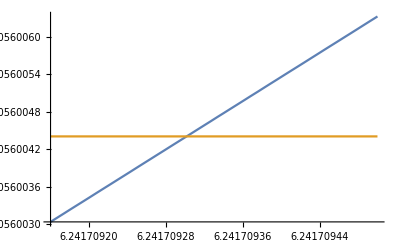

```mathematica
Plot[{Log[1+α]/Log[1+2*α],0.7610560044063083},{α,6.24170916,6.2417095}]
```

```mathematica
Solve[Dh[6.24170916,β,1]==0.4]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{β→2.8887}}

```mathematica
{Dh[α,β,0],Dh[α,β,1],Dh[α,β,2]}/.{α->6.24170916,β->2.8887033412743923}
```

{1,0.4,0.3}

## Question 6

```mathematica
disc={1,δ}
```

{1,δ}

```mathematica
disc.{2,20}==disc.{3,20-x}
```

2+20 δ==3+(20-x) δ

```mathematica
Solve[2+20 δ==3+(20-x) δ,x][[1]]
```

{x→1/δ}

## Question 7

```mathematica
disc.{20,2}==disc.{21,2-x}
```

20+2 δ==21+(2-x) δ

```mathematica
Solve[disc.{20,2}==disc.{21,2-x},x][[1]]
```

{x→1/δ}

## Question 8

```mathematica
F[u_,U_,δ_,θ_]:=((1-δ)*u^θ+δ*U^θ)^(1/θ)
```

```mathematica
uflow={2,20}
U2=0
U1=F[uflow[[2]],0,1/2,1/2]
U0=F[uflow[[1]],U1,1/2,1/2]
U[2,20]=U0;
```

{2,20}

0

5

(1/(√2)+(√5)/2)^2

(1/(√2)+(√5)/2)^2

```mathematica
uflow={3,20-x}
U2=0
U1=F[uflow[[2]],0,1/2,1/2]
U0=F[uflow[[1]],U1,1/2,1/2]
U[3,20-x]=U0
```

{3,20-x}

0

(20-x)/4

((√3)/2+(√(20-x))/4)^2

((√3)/2+(√(20-x))/4)^2

```mathematica
U[2,20]==U[3,20-x]
NSolve[U[2,20]==U[3,20-x]][[1]]
```

(1/(√2)+(√5)/2)^2==((√3)/2+(√(20-x))/4)^2

{x→5.28156}

## Question 8

Recursive Utility ⟶ the present utility at period t is a function of the instantaneous utility at period t and the present utility at t+1:

```mathematica
F[u_,U_,δ_,θ_]:=((1-δ)*u^θ+δ*U^θ)^(1/θ)
```

```mathematica
uflow={2,20}
U2=0
U1=F[uflow[[2]],0,1/2,1/2]
U0=F[uflow[[1]],U1,1/2,1/2]
U[2,20]=U0;
```

{2,20}

0

5

(1/(√2)+(√5)/2)^2

(1/(√2)+(√5)/2)^2

```mathematica
uflow={3,20-x}
U2=0
U1=F[uflow[[2]],0,1/2,1/2]
U0=F[uflow[[1]],U1,1/2,1/2]
U[3,20-x]=U0
```

{3,20-x}

0

(20-x)/4

((√3)/2+(√(20-x))/4)^2

((√3)/2+(√(20-x))/4)^2

```mathematica
U[2,20]==U[3,20-x]
NSolve[U[2,20]==U[3,20-x]][[1]]
```

(1/(√2)+(√5)/2)^2==((√3)/2+(√(20-x))/4)^2

{x→5.28156}

## Question 9

```mathematica
uflow={20,2}
U2=0
U1=F[uflow[[2]],0,1/2,1/2]
U0=F[uflow[[1]],U1,1/2,1/2]
U[20,2]=U0;
```

{20,2}

0

1/2

(1/(2 √2)+√5)^2

```mathematica
uflow={21,2-x}
U2=0
U1=F[uflow[[2]],0,1/2,1/2]
U0=F[uflow[[1]],U1,1/2,1/2]
U[21,2-x]=U0;
```

{21,2-x}

0

(2-x)/4

((√21)/2+(√(2-x))/4)^2

```mathematica
U[20,2]==U[21,2-x]
NSolve[U[20,2]==U[21,2-x]][[1]]
```

(1/(2 √2)+√5)^2==((√21)/2+(√(2-x))/4)^2

{x→0.575954}

## Bonus: Can we make computing recursive utility more efficient?

```mathematica
Exit[]
```

```mathematica
ClearAll[RecUtil]
RecUtil[u_List,F_,δ_,θ_]:=Module[{T=Length[u]-1,U},(*Initialize U as a list of the same length as u*)U=ConstantArray[0,Length[u]];
(*Set U_T=F[u_T,0]*)U[[T+1]]=F[u[[T+1]],0,δ,θ];
(*Recursively compute U_t for t=T-1,T-2,...,0*)Do[U[[t+1]]=F[u[[t+1]],U[[t+2]],δ,θ],{t,T-1,0,-1}];
(*Return U_0*)U[[1]]]
```

```mathematica
F[u_,U_,δ_,θ_]:=((1-δ)*u^θ+δ*U^θ)^(1/θ)
F[u,U,δ,θ]
```

(u^θ (1-δ)+U^θ δ)^(1/θ)

```mathematica
RecUtil[{20,2},F,1/2,1/2]
RecUtil[{21,2-x},F,1/2,1/2]
RecUtil[{2,20},F,1/2,1/2]
RecUtil[{3,20-x},F,1/2,1/2]
```

(1/(2 √2)+√5)^2

((√21)/2+(√(2-x))/4)^2

(1/(√2)+(√5)/2)^2

((√3)/2+(√(20-x))/4)^2